## SAM averages of temp

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
tempSAM=Import["temperatureSAM_SAM_averaged.dat"];
```

```mathematica
nx=tempSAM[[1,1]];ny=tempSAM[[1,2]];nz=tempSAM[[1,3]];
```

```mathematica
tempSAM=Delete[tempSAM,1]
```

{{0.,0.,0.,0.756567,0.827474,0.915088,0.638201,0.,0.,0.,0.,0.135176,1.05712,1.03179,1.08372,1.08992,1.04385,0.943413,0.133175,0.,0.,1.04296,1.10323,1.03906,1.02519,0.973735,0.957069,1.06571,1.00996,0.,0.663803,1.0868,1.03323,0.923668,0.948423,0.950699,0.975292,1.03941,1.05805,0.686063,0.880335,1.03462,0.967024,0.956822,0.922175,0.929068,0.925892,1.04124,0.984382,0.89198,0.865872,1.0481,1.04747,0.960786,0.912324,0.919833,0.969562,1.04696,1.02387,0.999081,0.719052,1.04817,0.956376,1.03248,0.933212,0.935083,0.984956,1.01167,1.07463,0.570326,0.,1.00669,1.08059,1.01935,1.00318,1.02992,1.0122,1.03736,1.00955,0.,0.,0.232642,1.02386,1.09253,1.04513,1.05383,1.07272,1.02657,0.129642,0.,0.,0.,0.,0.655147,0.831503,0.894194,0.644642,0.,0.,0.,0.,0.,0.,0.552286,0.956462,0.893245,0.694304,0.,0.,0.,0.,0.205596,1.04073,1.02726,1.02287,0.981219,1.07716,1.06636,0.180764,0.,0.,1.01302,1.06369,1.06414,1.02313,1.00701,1.04605,1.06905,1.04724,0.,0.696032,1.04945,1.02868,0.940901,0.987212,0.975385,0.99733,0.954991,1.06758,0.739889,0.978565,1.06671,1.04312,0.970566,0.988397,0.932938,0.997776,1.00369,1.04075,0.847454,0.929232,1.05029,1.03231,0.921,0.996015,0.927765,1.00843,1.07699,1.02578,0.891912,0.780251,1.11296,0.995651,0.986466,0.937728,0.981609,0.982454,1.03167,1.1136,0.613908,0.,1.02157,0.981129,1.05721,1.01489,1.04142,1.04078,1.04058,1.06832,0.,0.,0.124444,1.03831,1.1393,0.995671,1.06136,1.03395,1.04038,0.136897,0.,0.,0.,0.,0.69784,0.955418,0.814073,0.590962,0.,0.,0.,0.,0.,0.,0.660448,0.987921,0.957799,0.684754,0.,0.,0.,0.,0.230982,1.05828,1.06477,1.04652,1.10658,1.11033,1.03211,0.13575,0.,0.,0.923501,1.01058,1.02401,1.04085,1.01485,1.00682,1.08974,1.0618,0.,0.657871,0.99785,1.0123,0.958022,0.962587,1.06981,0.928224,1.06376,1.01591,0.682133,0.900573,1.06612,1.03137,0.980151,0.982935,0.944757,0.953633,1.01614,1.05197,0.93688,0.972631,0.982704,1.01364,1.00541,0.945464,0.919549,0.993141,0.98724,1.03193,0.999706,0.833863,1.08557,1.01967,0.956232,0.965813,0.966588,0.962161,1.02172,1.00233,0.710009,0.,0.949671,1.13555,1.06616,0.934281,1.05292,1.07497,1.06326,0.942941,0.,0.,0.168535,1.01683,1.08004,1.10975,1.05902,1.0981,0.979697,0.301033,0.,0.,0.,0.,0.705898,0.961193,0.879467,0.7704,0.,0.,0.,0.,0.,0.,0.690743,1.0183,0.996685,0.560037,0.,0.,0.,0.,0.184971,1.0754,1.05587,1.02885,1.07086,1.17304,1.12676,0.13512,0.,0.,1.06087,1.07615,1.04648,0.963713,0.946169,0.970578,1.0784,1.04834,0.,0.720591,1.05873,0.986668,0.975401,0.982416,0.972092,0.965077,1.01222,1.09639,0.740738,0.993027,1.0483,1.0297,1.01534,0.930496,0.940235,0.946633,1.0632,1.04524,0.948559,0.959552,1.15166,1.00621,0.948139,0.99741,0.953515,1.00809,1.01503,1.01806,0.91584,0.679242,1.0887,1.05808,1.01934,0.941158,0.965768,0.933741,1.10424,1.1193,0.662545,0.,1.01426,1.05551,1.03081,0.964088,1.01391,0.981526,1.02082,1.04366,0.,0.,0.121881,1.01677,1.12442,1.05073,1.0802,1.09759,1.06105,0.177643,0.,0.,0.,0.,0.750764,0.957356,0.841321,0.714984,0.,0.,0.,0.,0.,0.,0.596819,0.988182,0.991426,0.628191,0.,0.,0.,0.,0.161266,1.01817,1.09228,1.05942,1.09719,1.02782,1.02023,0.152707,0.,0.,1.00512,1.09178,1.01741,1.03145,0.984292,1.07173,1.0656,0.994344,0.,0.742887,1.13218,0.988607,0.967463,0.935765,0.953397,0.999247,1.03815,1.10556,0.691259,1.02294,1.08221,0.937592,0.970531,0.937325,0.960588,1.01269,1.01595,1.07923,0.895118,0.908378,1.03525,0.969928,0.959146,0.977918,0.999529,0.944006,0.979413,1.09753,0.948013,0.640564,1.08235,1.00881,0.97105,0.965842,0.944459,0.932535,1.08256,1.12763,0.694645,0.,1.09036,1.03116,1.01754,1.04593,1.02319,1.02319,1.09237,1.04323,0.,0.,0.135345,1.07724,1.03256,1.06034,1.04796,1.09298,1.06242,0.237005,0.,0.,0.,0.,0.543616,0.926678,0.899201,0.688829,0.,0.,0.,0.,0.,0.,0.62244,0.928161,0.953973,0.654249,0.,0.,0.,0.,0.171222,1.07325,1.12806,0.990897,1.12019,1.11898,1.02789,0.161713,0.,0.,1.00681,0.991452,0.994333,1.03904,1.00801,1.09165,1.01202,1.12452,0.,0.730228,1.02817,1.01709,0.941168,0.998969,0.935185,0.996624,1.08537,1.0305,0.624045,0.853385,1.041,1.01878,0.968727,0.944096,0.954189,0.989632,0.951347,1.03105,0.875367,0.987081,1.0215,0.970492,1.00839,0.956888,0.923755,0.984128,1.00578,1.0619,0.920567,0.776256,1.03374,1.05953,1.00051,0.957633,0.960538,0.955632,0.989069,1.06209,0.734854,0.,1.00961,1.10613,1.02896,1.05983,1.05405,1.1204,1.07025,1.00389,0.,0.,0.168978,0.949754,1.06236,1.10606,1.09312,1.07497,0.995751,0.197059,0.,0.,0.,0.,0.686793,0.847494,0.929961,0.627431,0.,0.,0.,0.,0.,0.,0.724196,0.852453,0.845842,0.713087,0.,0.,0.,0.,0.160175,1.06454,1.01377,1.06487,1.01013,0.99268,1.02952,0.12385,0.,0.,1.0285,1.08334,0.982159,1.06416,1.00184,1.07195,1.02466,1.06049,0.,0.787018,1.13596,0.94226,0.981185,0.97076,0.905503,0.958414,1.05328,1.02368,0.659205,0.963216,1.04412,1.04001,0.935828,0.998064,0.983039,1.01244,0.953979,1.04904,0.918585,0.957927,1.08726,1.01381,0.912754,0.924816,0.950527,0.951103,1.00176,1.15011,0.971015,0.773991,1.06124,1.00096,0.985064,1.00654,0.955049,0.978956,1.0476,1.06832,0.734243,0.,1.02609,1.03894,0.987272,1.03815,1.00209,1.0102,1.05876,1.10481,0.,0.,0.174815,1.00173,1.14757,1.09072,1.05743,1.10688,0.984963,0.07046,0.,0.,0.,0.,0.708191,0.875826,0.980976,0.788088,0.,0.,0.,0.,0.,0.,0.674497,1.00013,0.951895,0.79552,0.,0.,0.,0.,0.194028,1.03914,1.08889,1.05758,1.14471,1.09209,1.03,0.234268,0.,0.,1.06383,1.08798,0.939751,1.02795,0.988983,1.01059,1.10707,1.04034,0.,0.569771,1.08255,1.00911,1.01711,0.971607,1.0288,0.972605,1.01182,1.03613,0.604593,0.889385,1.13666,0.977469,0.939061,0.947593,0.863415,0.984759,1.03127,1.09296,0.914545,1.00407,1.04497,1.01648,0.989888,0.918098,0.993182,0.954287,0.99233,1.04939,0.848213,0.546513,1.05756,1.04439,1.01271,0.924735,0.978943,1.03044,1.08286,1.06979,0.624956,0.,0.994784,0.959552,0.979069,1.03404,1.00406,1.00485,1.08224,1.00427,0.,0.,0.126698,0.999263,1.05167,1.08611,0.984596,1.09833,1.05821,0.188132,0.,0.,0.,0.,0.706593,0.957377,0.851545,0.757981,0.,0.,0.,0.,0.,0.,0.866192,0.924028,0.966721,0.784817,0.,0.,0.,0.,0.102122,1.02441,0.99769,1.0299,1.05388,1.06469,1.01754,0.07136,0.,0.,1.08723,1.06872,1.05512,1.04151,1.02993,1.0187,1.08197,0.996802,0.,0.675227,1.02206,0.994579,1.00908,0.974651,0.980156,1.01701,0.977389,1.05661,0.745803,0.906894,1.02071,0.942973,0.96566,0.927296,0.99868,0.939808,1.02895,1.08976,0.854238,0.935458,1.06542,1.05085,0.919595,0.928156,0.949484,0.944812,0.98427,1.03108,0.875921,0.735256,1.08066,1.01257,1.02528,0.929176,0.954367,0.984622,1.02424,1.03259,0.680096,0.,1.09376,1.05389,1.05846,0.980392,0.99517,1.15438,1.04044,0.990862,0.,0.,0.145257,1.09936,1.05616,1.08249,1.06014,1.08993,1.07847,0.130406,0.,0.,0.,0.,0.68215,0.97415,0.900763,0.660666,0.,0.,0.,0.,0.,0.,0.710917,0.94235,1.0222,0.615549,0.,0.,0.,0.,0.150795,1.04783,1.0817,1.01478,1.04679,1.01122,1.07286,0.18876,0.,0.,1.09679,1.09077,1.05264,0.988195,1.03236,1.00783,1.09537,1.02716,0.,0.855554,1.03008,0.985408,0.902523,0.970639,0.938358,1.00043,1.04541,1.10291,0.731489,0.994459,1.06024,0.988747,0.938728,0.9614,0.949151,0.923718,1.02692,1.03455,0.953476,0.903998,1.06982,1.06261,0.994979,0.944454,0.901123,0.997862,1.0046,1.08356,0.902082,0.742578,1.0853,1.01781,0.987283,0.960317,0.92949,0.953007,0.997965,1.07119,0.725495,0.,1.0179,1.08461,1.05052,1.04111,1.05119,1.01997,1.07393,1.00375,0.,0.,0.159004,1.06134,1.14124,0.993914,1.0066,1.03318,0.992217,0.126087,0.,0.,0.,0.,0.588674,0.913129,0.932186,0.749803,0.,0.,0.,0.,0.,0.,0.733056,0.948068,0.901683,0.727368,0.,0.,0.,0.,0.23799,1.10433,1.11841,1.08346,1.06158,1.09146,0.976727,0.195977,0.,0.,1.05887,1.03426,1.057,0.975142,1.03654,1.02037,1.06782,0.997357,0.,0.727579,1.06031,1.05201,0.985507,0.949639,1.0072,0.995958,1.01687,1.05606,0.657495,0.920811,1.05596,1.05764,1.03963,0.962218,0.980988,1.02201,0.960311,1.06053,1.008,0.838255,1.01182,0.963493,1.012,0.947672,0.950494,0.95876,0.961777,0.999507,0.956425,0.6627,1.05521,1.0158,0.983335,1.01423,0.960932,0.998336,1.06963,1.07569,0.71345,0.,0.986637,1.07199,0.974535,1.04126,0.958777,1.03211,1.02983,1.04416,0.,0.,0.140277,1.10047,1.05956,1.03693,1.06616,1.0901,1.04546,0.134716,0.,0.,0.,0.,0.578812,1.03424,0.858658,0.648343,0.,0.,0.,0.,0.,0.,0.858333,0.881942,0.980882,0.695988,0.,0.,0.,0.,0.105875,0.990492,1.07621,1.02135,1.08751,1.07326,1.07946,0.123647,0.,0.,0.995514,1.0328,1.02565,0.990345,0.9762,1.05548,1.04382,1.13925,0.,0.559033,1.01856,1.00877,0.962847,0.951954,0.952066,0.963143,1.03798,1.02802,0.742751,0.969387,1.01426,0.971747,0.919395,0.938262,0.87375,0.933533,1.03192,1.06087,0.979977,0.96551,1.03827,1.00323,0.975519,0.96407,0.948502,0.927904,0.963182,1.04496,0.899169,0.863275,1.01726,1.08195,0.959886,1.00612,0.930884,1.04228,1.03758,1.04874,0.585047,0.,1.15001,1.04849,1.05961,1.06832,0.94264,0.946304,1.04319,0.945553,0.,0.,0.129082,0.995795,1.04905,1.07922,1.08521,1.02822,1.02518,0.144111,0.,0.,0.,0.,0.734219,0.92903,0.943845,0.783981,0.,0.,0.,0.,0.,0.,0.568944,0.874814,0.972411,0.658348,0.,0.,0.,0.,0.206655,1.0252,1.08553,1.05758,1.03068,1.08734,1.1341,0.275777,0.,0.,1.00713,1.04709,1.01423,1.0725,1.07963,1.07223,1.09324,1.05646,0.,0.667122,1.06127,1.10774,1.02909,0.982338,0.989337,0.98644,1.02952,0.988304,0.617225,0.972869,1.04969,1.09776,1.01689,0.914998,0.980644,0.929164,0.990114,1.01419,0.9227,0.960829,1.04847,1.01743,0.979599,0.981046,0.911007,0.980764,1.02465,1.03219,0.880602,0.734281,1.07816,1.05005,0.957374,0.967909,0.946739,0.937371,1.1081,1.02151,0.717512,0.,0.983075,1.10494,1.06422,0.991248,0.98557,1.08096,1.05726,1.03395,0.,0.,0.144512,1.02025,1.06893,1.02331,1.03144,1.05926,1.03689,0.286868,0.,0.,0.,0.,0.694215,0.952967,0.9804,0.588499,0.,0.,0.,0.,0.,0.,0.762322,0.97763,1.00711,0.621623,0.,0.,0.,0.,0.175076,0.985953,1.05773,1.05723,1.07532,1.05059,1.02377,0.168367,0.,0.,1.06596,1.06749,1.05353,1.01863,0.981589,1.0912,1.10515,0.988701,0.,0.496706,1.05613,1.04109,1.00176,0.953773,1.00503,0.930615,0.987497,1.03641,0.666914,0.891744,1.06723,1.01998,1.02039,0.964924,0.983579,0.949817,1.08456,0.99426,0.880184,0.900194,1.08744,1.04518,0.97058,0.964407,0.951112,1.00084,0.984982,1.00044,0.92266,0.608435,0.969141,1.07957,1.01332,0.970746,0.946976,0.990413,0.978667,1.03755,0.740391,0.,1.01307,1.03407,1.03175,1.01657,0.996528,1.0106,1.08248,1.06941,0.,0.,0.093381,1.03298,1.05767,1.10139,1.08551,1.07732,1.08611,0.143901,0.,0.,0.,0.,0.646201,0.999763,0.916134,0.634622,0.,0.,0.,0.,0.,0.,0.641549,1.04171,0.974229,0.604827,0.,0.,0.,0.,0.100606,1.075,1.06754,1.10718,1.04166,1.01133,1.04227,0.153581,0.,0.,0.96869,1.02254,1.02671,0.998449,0.957608,1.0313,1.05502,0.993241,0.,0.689483,1.05352,1.06871,1.00953,1.02727,0.934557,0.97784,1.02625,1.08817,0.596255,0.839326,1.07892,0.999378,0.979828,0.932135,0.897674,0.963385,1.03783,1.0096,0.90076,0.983077,1.13078,0.969297,0.974605,0.918158,0.962202,0.989884,1.00655,1.04921,0.935471,0.704222,1.0788,1.06406,0.962799,0.911331,0.912554,0.973549,1.03335,1.03755,0.88432,0.,1.04928,1.07171,0.996198,0.990333,0.994317,1.04437,1.05671,0.960465,0.,0.,0.159455,1.03182,1.07209,1.06572,1.12104,1.08395,1.05216,0.123846,0.,0.,0.,0.,0.651508,0.93435,0.992157,0.711035,0.,0.,0.,0.,0.,0.,0.647103,0.891223,0.945531,0.730364,0.,0.,0.,0.,0.12324,0.981439,1.02647,1.03001,1.06378,1.09669,1.08694,0.157504,0.,0.,1.10386,1.07376,1.03236,1.01336,1.01552,1.01774,1.03427,1.03761,0.,0.733685,1.02711,1.02052,1.02282,0.941034,0.930659,1.01417,1.04987,1.14989,0.774812,0.819797,1.06687,0.978416,0.921273,0.895744,0.887219,0.994332,1.0204,1.03265,0.877712,0.932803,0.994537,1.00559,1.00199,0.922325,0.95213,0.972902,1.06522,1.10349,0.925464,0.674445,1.03491,1.03276,0.980405,0.998136,0.957351,0.933811,1.04085,1.09238,0.799729,0.,1.0489,1.0533,0.994664,1.0539,1.01488,1.03257,1.05765,1.01505,0.,0.,0.162086,0.9441,1.05351,1.06391,1.06047,1.08375,1.11941,0.17404,0.,0.,0.,0.,0.787903,0.946781,0.890507,0.734498,0.,0.,0.,0.,0.,0.,0.670761,1.00626,0.924948,0.752303,0.,0.,0.,0.,0.230279,0.989487,1.00254,1.08932,1.02458,1.11132,1.11881,0.184016,0.,0.,1.0401,1.08997,1.05441,0.988803,1.01578,0.989993,0.986802,1.00146,0.,0.707582,1.10283,1.05619,0.972664,0.955182,0.907885,0.971269,1.06334,1.08059,0.709175,0.874062,1.04681,0.979801,0.915566,0.982198,0.917954,0.951638,1.01811,1.08091,0.983958,0.861558,1.0779,0.987013,0.966621,0.933229,0.95241,0.975527,0.974251,1.03913,0.96101,0.620762,1.06252,0.993094,1.06016,0.963649,0.926207,0.989345,1.05413,1.03562,0.659988,0.,1.10786,1.02521,1.06023,0.990523,0.997183,0.990778,1.03389,0.992566,0.,0.,0.278686,1.08594,1.03142,1.05415,0.995049,1.10074,1.0532,0.243128,0.,0.,0.,0.,0.758401,0.890348,0.884926,0.726665,0.,0.,0.,0.,0.,0.,0.75364,0.93324,0.964496,0.614283,0.,0.,0.,0.,0.191912,0.972531,1.10657,1.06914,0.974908,1.03796,1.02292,0.177452,0.,0.,1.03564,1.0762,1.0114,1.02893,1.03848,1.03132,1.02174,1.02191,0.,0.633193,1.05469,1.0527,0.971404,0.926968,0.94962,0.938722,1.0082,1.06302,0.682546,0.841679,1.1207,0.958271,0.966381,0.906046,0.965273,0.919739,1.00344,1.01749,0.88465,0.913894,1.07981,1.04192,0.87294,0.955698,0.961202,0.999002,0.991151,1.03263,0.885965,0.77968,1.01846,1.04633,0.988475,0.968401,0.907164,0.982539,0.998086,1.0588,0.573808,0.,1.02733,1.08236,1.00777,1.01726,0.974522,1.09037,1.02392,0.998719,0.,0.,0.123252,1.02726,1.05412,1.09611,0.960658,1.07818,1.13879,0.151808,0.,0.,0.,0.,0.745362,0.894165,0.961381,0.674205,0.,0.,0.,0.,0.,0.,0.760187,0.885137,0.904007,0.613048,0.,0.,0.,0.,0.076222,0.983789,1.06957,1.04058,1.08242,1.08144,1.00089,0.125067,0.,0.,1.12698,1.06785,1.06445,0.985296,1.03808,1.01289,1.11611,1.0253,0.,0.725446,1.05219,1.03107,1.0172,0.987495,0.945545,0.972486,1.05166,1.04963,0.632403,0.978518,1.05514,1.0849,0.926192,0.957151,0.942065,1.00338,1.01739,1.01173,0.922992,0.991827,1.10705,1.0391,0.99121,0.944012,0.944098,1.00693,1.0875,1.05856,1.00766,0.690926,1.02446,1.04542,1.02997,0.930425,0.986518,0.98717,1.02562,1.10917,0.64547,0.,1.00256,0.978099,1.01362,0.973461,0.99872,1.09765,1.07147,1.01276,0.,0.,0.18187,0.993554,1.07619,1.04883,0.996261,1.09122,0.988904,0.115786,0.,0.,0.,0.,0.722112,0.953552,0.947792,0.808824,0.,0.,0.,0.,0.,0.,0.718986,0.983335,0.947565,0.609862,0.,0.,0.,0.,0.270818,1.06823,1.09323,1.02731,1.00139,1.08406,0.988145,0.219582,0.,0.,1.05115,1.06657,1.11477,0.946442,0.990955,0.978108,1.09671,1.01586,0.,0.635581,1.04204,1.01286,1.00847,0.968635,0.974985,1.0243,1.01871,1.03922,0.806081,0.875153,1.05809,1.06089,0.920339,0.968901,0.909206,0.985955,0.985125,1.06965,0.877215,0.822711,0.948902,1.05227,0.921207,0.963195,0.928439,0.920549,1.00994,1.07931,1.11616,0.706189,1.10417,1.04238,0.980407,0.977287,1.01574,0.939415,1.08138,1.03184,0.738926,0.,1.05281,1.06289,1.03452,1.01209,1.05838,1.0413,1.06802,1.08799,0.,0.,0.203187,1.06643,1.0813,1.12895,1.05697,1.02172,0.983964,0.142416,0.,0.,0.,0.031511,0.638174,0.857291,0.962612,0.623559,0.,0.,0.,0.,0.,0.,0.862589,0.956508,0.90026,0.785003,0.,0.,0.,0.,0.131455,1.01663,1.13271,1.0209,1.12276,1.0506,1.0153,0.137158,0.,0.,0.983278,1.05401,1.00713,1.03247,0.998457,1.017,1.08997,0.998959,0.,0.712901,1.04612,0.975594,1.00734,0.992364,0.924869,1.01016,1.04393,1.0913,0.685368,0.889162,1.11181,1.01538,0.944892,0.957182,0.92734,0.948472,1.00152,1.06359,0.968887,0.909653,1.01558,1.02465,1.00759,0.93598,0.916018,0.926101,0.989198,1.11246,0.951416,0.692619,1.07473,1.03146,0.946818,0.921367,0.958164,0.979356,1.00437,1.03749,0.798813,0.,1.02929,1.06196,0.922977,0.952081,0.959471,1.04128,1.02467,1.04315,0.,0.,0.146324,1.02389,1.08591,1.04917,1.05836,1.08031,0.937043,0.203595,0.,0.,0.,0.,0.784822,0.926427,0.908619,0.650142,0.,0.,0.,0.,0.,0.,0.68163,0.92492,0.888668,0.648344,0.,0.,0.,0.,0.115875,0.96424,1.08257,1.02988,1.10833,1.02989,1.05359,0.12301,0.,0.,0.965544,0.967649,0.988255,1.02406,0.994456,1.03915,1.06932,0.981902,0.,0.679146,1.1042,0.988445,0.973796,0.920223,0.969719,0.953562,0.976609,1.02696,0.700598,0.906699,1.12606,0.987983,0.970641,0.939705,0.951159,1.00026,0.970667,1.0717,1.01269,0.966928,1.05768,1.0492,0.929386,0.936741,0.929039,0.926575,0.981795,1.09538,0.974898,0.83946,1.07915,1.03722,0.972098,0.926327,0.963015,1.00075,1.0062,1.06737,0.63784,0.,1.0922,1.07798,1.05401,0.994867,0.96456,0.943548,1.08505,1.01613,0.,0.,0.169515,1.08998,1.07576,1.04669,1.04376,1.03386,1.00555,0.178056,0.,0.,0.,0.,0.671957,0.988316,0.950411,0.671212,0.,0.,0.,0.,0.,0.,0.546112,1.07419,0.953512,0.733357,0.,0.,0.,0.,0.101798,1.01702,1.16289,1.06722,1.08322,1.10783,1.03757,0.151039,0.,0.,0.993162,1.06818,1.05283,0.968662,0.967494,1.0269,0.997384,1.05276,0.,0.627545,1.03487,1.01133,0.959328,0.935624,0.941574,0.97116,1.00686,1.02064,0.79223,0.9269,1.05853,0.966181,0.929936,0.988156,0.951233,1.00857,0.991222,1.05829,0.989842,0.938575,1.02364,1.04196,0.93061,0.949349,0.953331,0.979164,0.972102,1.03129,0.880576,0.773744,1.05549,1.0214,0.981281,0.985856,0.989716,0.969717,1.05512,1.16419,0.688353,0.,0.96088,1.08084,1.04214,0.991392,1.02952,1.02367,1.04153,1.12127,0.,0.,0.13491,1.06431,1.05756,0.97372,1.0497,1.02474,0.946574,0.07019,0.,0.,0.,0.,0.90998,0.878687,0.930837,0.626002,0.,0.,0.,0.,0.,0.,0.631532,0.928546,1.06222,0.667435,0.,0.,0.,0.,0.150891,1.01036,1.06945,1.07127,1.02388,1.11238,1.05306,0.120724,0.,0.,1.02605,1.06331,1.00113,0.974524,1.0029,1.02183,1.03947,0.971489,0.,0.728117,1.04241,1.01217,0.992583,0.966016,0.943432,1.02299,1.04206,1.05823,0.733452,0.920597,1.04822,1.02438,0.92089,0.916717,0.90537,0.986707,0.970516,1.07754,0.890538,0.910419,1.01007,1.02895,1.02076,0.939353,0.909015,0.983846,1.00476,1.0565,0.863891,0.827064,1.04629,1.06186,0.999357,0.959691,0.961844,1.00567,1.01824,0.97372,0.695839,0.,1.07465,1.05527,1.04033,1.06728,1.02222,0.969645,0.985437,0.975228,0.,0.,0.137373,1.01885,1.09451,1.08814,1.08568,1.01957,1.01746,0.132023,0.,0.,0.,0.,0.606755,1.08134,0.917929,0.613417,0.,0.,0.,0.,0.,0.,0.639961,0.965813,0.974089,0.918342,0.,0.,0.,0.,0.19385,0.976202,1.04674,1.05052,1.00194,1.07092,1.08005,0.184763,0.,0.,1.02771,1.09364,1.08535,1.0089,0.931652,0.979336,1.00446,1.05918,0.,0.726015,1.16246,1.00597,1.02561,1.01773,0.923237,0.937503,1.02673,1.11025,0.755783,0.947636,1.0731,1.03141,1.00173,0.931046,0.940233,0.955215,0.992865,1.115,0.988004,0.8785,1.02808,0.966125,0.998216,0.929465,0.902117,0.952292,1.00761,1.01083,0.927853,0.598026,0.977173,0.976143,0.970977,0.964642,0.918959,1.01,1.01743,1.05084,0.690311,0.,1.02552,1.01259,0.984934,0.950415,0.958199,1.04922,0.996431,1.0255,0.,0.,0.184459,1.0476,1.09241,1.0178,1.10903,1.04693,1.09088,0.171746,0.,0.,0.,0.,0.76309,0.919599,0.948859,0.789967,0.,0.,0.,0.,0.,0.,0.690837,1.00274,0.93421,0.864352,0.,0.,0.,0.,0.255386,1.0598,1.05998,1.01384,1.07552,1.03868,1.02112,0.214634,0.,0.,0.93884,1.01782,1.05492,0.976321,0.996414,1.00605,1.05031,0.986713,0.,0.802124,0.999321,1.0802,0.971341,0.979098,0.973487,0.9779,1.02602,1.09751,0.746643,1.0145,1.02391,1.00228,0.988723,0.928559,0.982579,0.954594,1.02547,1.01625,1.00584,0.951396,1.03891,1.04804,0.92646,0.927251,0.96517,0.996214,0.973607,1.04876,0.888265,0.756716,1.17864,0.998493,0.95426,0.919728,0.963968,0.986948,1.0459,1.08489,0.563984,0.,1.1187,1.07405,1.00851,0.974892,0.994959,1.07734,1.0234,1.0615,0.,0.,0.195954,0.962997,1.0225,1.01465,1.06403,1.05947,1.03341,0.1541,0.,0.,0.,0.,0.735736,0.87499,0.975212,0.767251,0.,0.,0.,0.,0.,0.,0.724137,1.07627,0.896339,0.710042,0.,0.,0.,0.,0.203293,1.14286,1.06576,1.01112,1.03989,1.04512,1.103,0.199634,0.,0.,0.986115,1.04757,1.03482,0.981032,1.02009,0.961278,1.02166,1.09718,0.,0.755524,1.04383,1.05406,0.941343,0.955562,0.934664,0.919378,1.03075,1.12028,0.705403,0.883386,1.01692,1.0264,0.958155,0.935815,0.904387,0.960816,1.0114,1.07751,1.00672,1.00112,1.06675,1.02,0.965904,0.931385,0.952628,0.910665,1.04113,0.994672,0.899002,0.584984,1.08423,0.999255,1.0395,0.999576,0.989021,0.980887,1.08641,1.05897,0.724626,0.,0.964051,1.07308,0.978403,1.05501,1.03776,1.06698,0.994467,1.07408,0.,0.,0.096371,0.984857,1.05349,1.03974,1.08541,1.03472,1.02665,0.118304,0.,0.,0.,0.,0.563537,1.02246,0.941638,0.652691,0.,0.,0.,0.,0.,0.,0.813603,0.925706,0.961782,0.722332,0.,0.,0.,0.,0.185631,1.05128,1.08662,0.958099,1.05398,1.0455,0.995958,0.163135,0.,0.,1.03982,1.06418,0.981473,1.00634,1.00368,1.03188,1.07705,0.927705,0.,0.617406,1.06915,0.996143,0.935645,0.941331,0.935587,1.01748,1.08817,1.04461,0.728558,0.924665,1.0497,1.03715,0.899088,0.964319,0.898714,0.91458,1.01858,1.06387,1.04151,0.948245,1.04533,1.05892,0.951728,0.960947,0.942947,0.951239,1.01462,1.0195,0.882251,0.730702,1.0408,1.01626,0.991762,1.02627,0.955835,0.977649,1.02901,1.05876,0.648865,0.,1.06184,1.08944,0.963131,1.02761,1.01696,1.07955,1.07552,1.07795,0.,0.,0.213712,1.03558,1.12372,1.05109,1.08018,1.09282,1.07206,0.084431,0.,0.,0.,0.,0.691196,0.941953,0.896111,0.779025,0.,0.,0.,0.,0.,0.,0.824548,0.937174,0.927048,0.660081,0.,0.,0.,0.,0.139505,0.979215,1.05142,1.02752,1.12316,1.01947,1.00504,0.169918,0.,0.,1.04367,1.02847,1.0114,1.02722,0.995791,1.07201,1.03373,0.994143,0.,0.783807,1.05069,1.03278,1.04406,0.911303,0.957656,0.973661,1.0809,1.03042,0.75211,0.972661,1.04879,1.03262,0.946441,0.945395,0.983048,0.941198,0.98643,1.07001,1.00188,0.832141,1.01903,0.961082,0.986811,0.980223,0.925424,0.999575,0.989201,1.04495,1.02187,0.809044,1.05314,1.07857,0.98229,0.946522,0.948437,1.04214,1.03373,1.10894,0.730181,0.,1.02279,1.01928,1.03871,0.912362,0.990496,1.04122,1.0254,0.991681,0.,0.,0.369605,1.02954,1.05872,1.06991,1.10497,1.07884,1.0729,0.202953,0.,0.,0.,0.,0.67258,0.975744,0.832606,0.685841,0.,0.,0.,0.,0.,0.,0.630009,0.922614,0.972559,0.712211,0.,0.,0.,0.,0.092803,1.03474,1.01356,1.09287,1.0761,1.07603,1.10085,0.216538,0.,0.,1.02087,1.02933,1.03599,1.0139,0.990587,1.05259,1.07851,1.13118,0.,0.567994,1.09345,1.01172,0.959145,0.931156,0.974441,0.947931,0.987566,1.083,0.671072,0.888228,1.03379,1.04564,0.915536,0.972299,0.913323,0.976268,1.02721,1.05791,0.983683,0.92068,1.05136,0.972024,0.997107,0.961507,0.989907,0.996986,0.997893,1.03461,0.999678,0.807831,1.05196,1.04369,0.98009,0.973649,0.989143,1.00794,1.04434,1.06939,0.771075,0.,1.11409,1.01026,1.02809,1.00534,0.972632,1.04044,1.00779,0.988115,0.,0.,0.250453,1.03516,1.13955,1.04837,1.09033,1.10159,1.02479,0.238777,0.,0.,0.,0.,0.691404,0.912492,0.80161,0.682722,0.,0.,0.}}

```mathematica
slices=Partition[tempSAM[[1]],ny*nz];
```

```mathematica
crosssections=Array[cs,nx];
```

{cs[1],cs[2],cs[3],cs[4],cs[5],cs[6],cs[7],cs[8],cs[9],cs[10],cs[11],cs[12],cs[13],cs[14],cs[15],cs[16],cs[17],cs[18],cs[19],cs[20],cs[21],cs[22],cs[23],cs[24],cs[25],cs[26],cs[27],cs[28],cs[29],cs[30]}

```mathematica
Table[crosssections[[i]]=Partition[slices[[i]],nz],{i,1,nx}];
```

```mathematica
Length[%]
```

30

```mathematica
crosssections[[4]]//MatrixForm
```

(0. | 0. | 0. | 0.690743 | 1.0183 | 0.996685 | 0.560037 | 0. | 0. | 0.
0. | 0.184971 | 1.0754 | 1.05587 | 1.02885 | 1.07086 | 1.17304 | 1.12676 | 0.13512 | 0.
0. | 1.06087 | 1.07615 | 1.04648 | 0.963713 | 0.946169 | 0.970578 | 1.0784 | 1.04834 | 0.
0.720591 | 1.05873 | 0.986668 | 0.975401 | 0.982416 | 0.972092 | 0.965077 | 1.01222 | 1.09639 | 0.740738
0.993027 | 1.0483 | 1.0297 | 1.01534 | 0.930496 | 0.940235 | 0.946633 | 1.0632 | 1.04524 | 0.948559
0.959552 | 1.15166 | 1.00621 | 0.948139 | 0.99741 | 0.953515 | 1.00809 | 1.01503 | 1.01806 | 0.91584
0.679242 | 1.0887 | 1.05808 | 1.01934 | 0.941158 | 0.965768 | 0.933741 | 1.10424 | 1.1193 | 0.662545
0. | 1.01426 | 1.05551 | 1.03081 | 0.964088 | 1.01391 | 0.981526 | 1.02082 | 1.04366 | 0.
0. | 0.121881 | 1.01677 | 1.12442 | 1.05073 | 1.0802 | 1.09759 | 1.06105 | 0.177643 | 0.
0. | 0. | 0. | 0.750764 | 0.957356 | 0.841321 | 0.714984 | 0. | 0. | 0.)

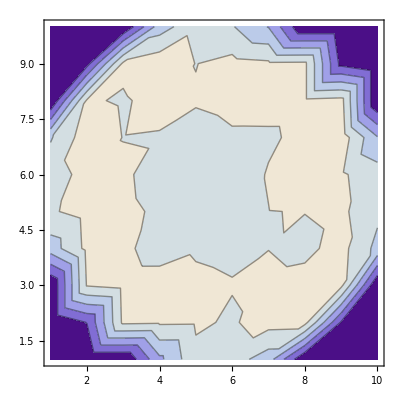

```mathematica
ListContourPlot[crosssections[[2]]]
```

```mathematica
a=1.0;
```

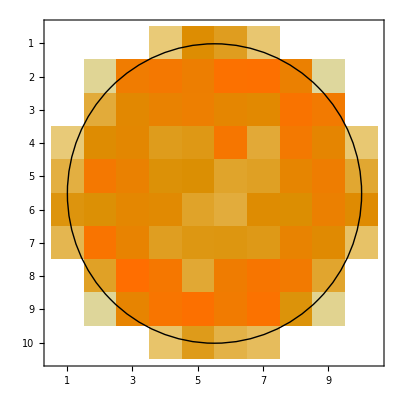

```mathematica
Show[MatrixPlot[crosssections[[3]]],Graphics[Circle[{ny/2,nz/2},(nz-a)/2]]]
```

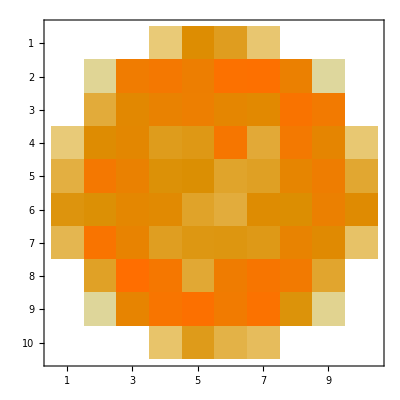

```mathematica
MatrixPlot[crosssections[[3]]]
```

```mathematica
ListPlot3D[crosssections]
```

-Graphics3D-

```mathematica
Mean[crosssections]
```

{{0.,0.,0.,0.700498,0.952109,0.949614,0.693941,0.,0.,0.},{0.,0.166183,1.03092,1.06859,1.04419,1.06247,1.06779,1.04354,0.165966,0.},{0.,1.02692,1.05601,1.03076,1.00922,1.00064,1.02539,1.05907,1.02964,0.},{0.689166,1.05997,1.0206,0.980266,0.963257,0.959498,0.977231,1.02938,1.06186,0.70207},{0.921352,1.06017,1.01183,0.958111,0.948052,0.938393,0.966221,1.00926,1.05075,0.938798},{0.928417,1.04795,1.01598,0.966698,0.948252,0.942848,0.970371,1.00452,1.04872,0.935088},{0.723089,1.0607,1.02965,0.990366,0.9618,0.956702,0.981126,1.03872,1.0655,0.691987},{0.,1.03701,1.05383,1.01979,1.00674,1.00454,1.03808,1.04547,1.02502,0.},{0.,0.169069,1.02919,1.07786,1.05729,1.05782,1.06953,1.03457,0.163639,0.},{0.,0.,0.00105037,0.692454,0.937154,0.912198,0.694876,0.,0.,0.}}

```mathematica
ListPlot3D[%]
```

-Graphics3D-

## CAM averages of temp

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
tempCAM=Import["temperatureCAM_CAM_averaged.dat"];
```

```mathematica
nx=tempCAM[[1,1]];ny=tempCAM[[1,2]];nz=tempCAM[[1,3]];
```

```mathematica
tempCAM=Delete[tempCAM,1];
```

```mathematica
tempCAM=Flatten[tempCAM];
```

```mathematica
slices=Partition[tempCAM,ny*nz];
```

```mathematica
crosssections=Array[cs,nx];
```

{cs[1],cs[2],cs[3],cs[4],cs[5],cs[6],cs[7],cs[8],cs[9],cs[10],cs[11],cs[12],cs[13],cs[14],cs[15],cs[16],cs[17],cs[18],cs[19],cs[20],cs[21],cs[22],cs[23],cs[24],cs[25],cs[26],cs[27],cs[28],cs[29],cs[30]}

```mathematica
Table[crosssections[[i]]=Partition[slices[[i]],nz],{i,1,nx}];
```

```mathematica
crosssections[[4]]//MatrixForm
```

(0. | 0. | 0. | 1.18611 | 1.30212 | 1.27472 | 1.19174 | 0. | 0. | 0.
0. | 1.0953 | 1.42209 | 1.6321 | 1.89203 | 1.8583 | 1.68961 | 1.35755 | 1.08033 | 0.
0. | 1.43308 | 1.7378 | 2.71154 | 3.27899 | 3.2855 | 2.61829 | 1.83264 | 1.35696 | 0.
1.16425 | 1.73158 | 2.5418 | 3.66779 | 4.94049 | 4.73458 | 3.88671 | 2.72468 | 1.57579 | 1.29093
1.38858 | 1.86729 | 3.27304 | 4.69502 | 5.61581 | 5.58116 | 4.78811 | 3.46834 | 1.83478 | 1.25719
1.21202 | 1.95739 | 3.32058 | 4.73328 | 5.66975 | 5.67669 | 4.75135 | 3.15189 | 1.74805 | 1.23955
1.12328 | 1.54066 | 2.73366 | 3.97743 | 4.94687 | 4.82275 | 3.90844 | 2.79541 | 1.5588 | 1.34548
0. | 1.28148 | 1.81709 | 2.71591 | 3.20388 | 3.33812 | 2.52516 | 1.71555 | 1.29955 | 0.
0. | 0.887731 | 1.3311 | 1.60861 | 1.82965 | 1.79267 | 1.62306 | 1.38599 | 1.54708 | 0.
0. | 0. | 0. | 1.22631 | 1.22703 | 1.22955 | 1.20928 | 0. | 0. | 0.)

```mathematica
ListPlot3D[crosssections]
```

-Graphics3D-

```mathematica
Mean[crosssections]
```

{{0.,0.,0.,0.700498,0.952109,0.949614,0.693941,0.,0.,0.},{0.,0.166183,1.03092,1.06859,1.04419,1.06247,1.06779,1.04354,0.165966,0.},{0.,1.02692,1.05601,1.03076,1.00922,1.00064,1.02539,1.05907,1.02964,0.},{0.689166,1.05997,1.0206,0.980266,0.963257,0.959498,0.977231,1.02938,1.06186,0.70207},{0.921352,1.06017,1.01183,0.958111,0.948052,0.938393,0.966221,1.00926,1.05075,0.938798},{0.928417,1.04795,1.01598,0.966698,0.948252,0.942848,0.970371,1.00452,1.04872,0.935088},{0.723089,1.0607,1.02965,0.990366,0.9618,0.956702,0.981126,1.03872,1.0655,0.691987},{0.,1.03701,1.05383,1.01979,1.00674,1.00454,1.03808,1.04547,1.02502,0.},{0.,0.169069,1.02919,1.07786,1.05729,1.05782,1.06953,1.03457,0.163639,0.},{0.,0.,0.00105037,0.692454,0.937154,0.912198,0.694876,0.,0.,0.}}

```mathematica
ListPlot3D[%]
```

-Graphics3D-